```mathematica
Guy F. Mongelli
```

```mathematica
The purpose of this notebook is to determine the weight percent alcohol for various number of molecules of of alcohol at a constant total number of molecules.
```

```mathematica
β=2783-α;
```

```mathematica
The molecular weights of alcohol and water respectively are:
```

```mathematica
xEtOH=46 (* g/mol *);
```

```mathematica
xMeOH=32 (* g/mol *);
```

```mathematica
xPOH=60.1 (* g/mol *);
```

```mathematica
y=18 (* g/mol *);
```

```mathematica
MassPerEt[α_]=(α*xEtOH)/(α*xEtOH+(β)*y)
```

(46 α)/(46 α+18 β)

```mathematica
MassPerMe[α_]=(α*xMeOH)/(α*xMeOH+(β)*y)
```

(32 α)/(32 α+18 β)

```mathematica
MassPerP[α_]=(α*xPOH)/(α*xPOH+(β)*y)
```

(60.1 α)/(60.1 α+18 β)

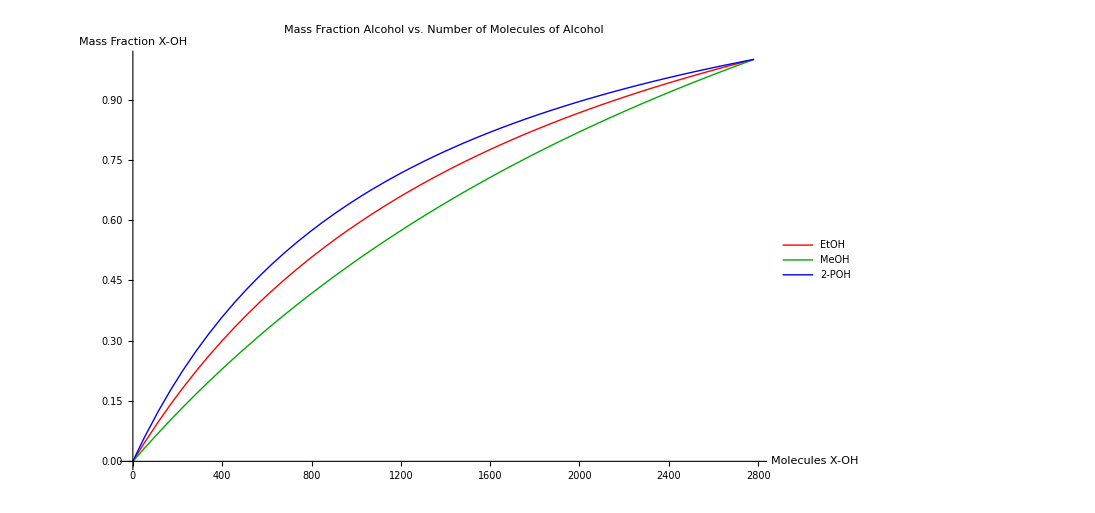

```mathematica
Plot[{MassPerEt[α],MassPerMe[α],MassPerP[α]},{α,0,2782},AxesLabel->{Style["Molecules X-OH",24],Style["Mass Fraction X-OH",24]},PlotLegends->{Style["EtOH",24],Style["MeOH",24],Style["2-POH",24]},PlotLabel->Style["Mass Fraction Alcohol vs. Number of Molecules of Alcohol",24],BaseStyle->{FontWeight->"Bold",FontSize->24},PlotStyle->{Red,Darker[Green],Blue}]
```

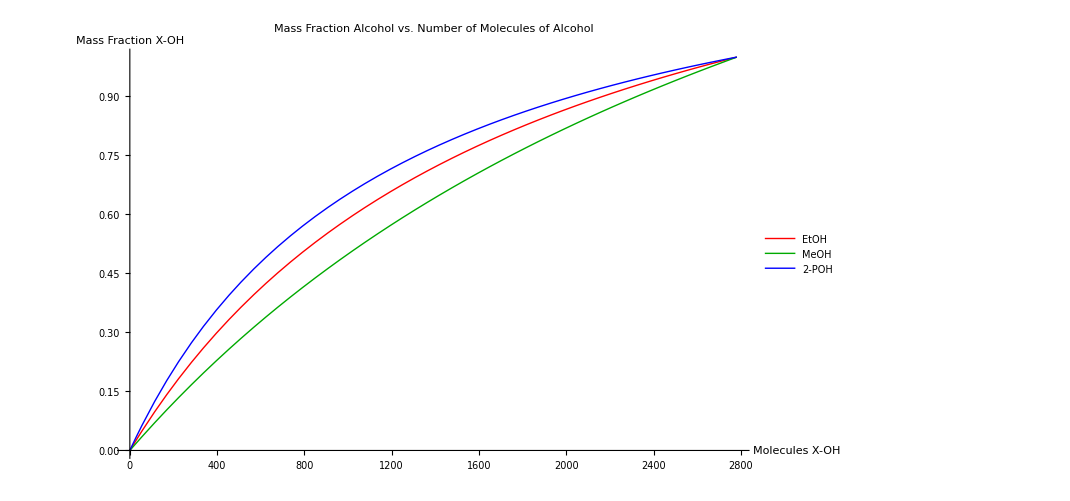
```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

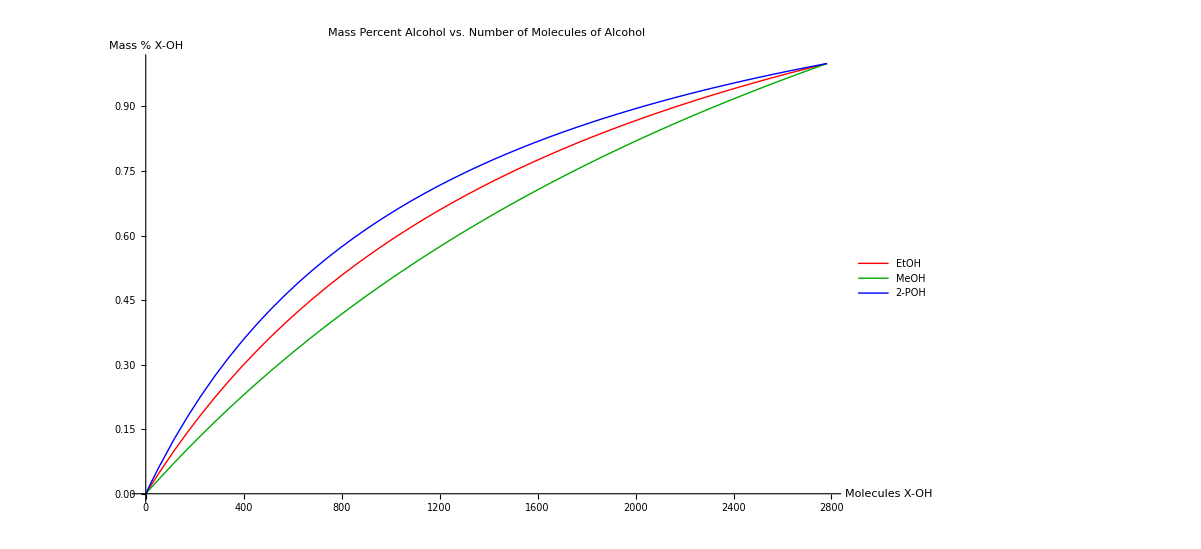
```mathematica
Export["graph.jpeg",-Graphics-]
```

graph.jpeg

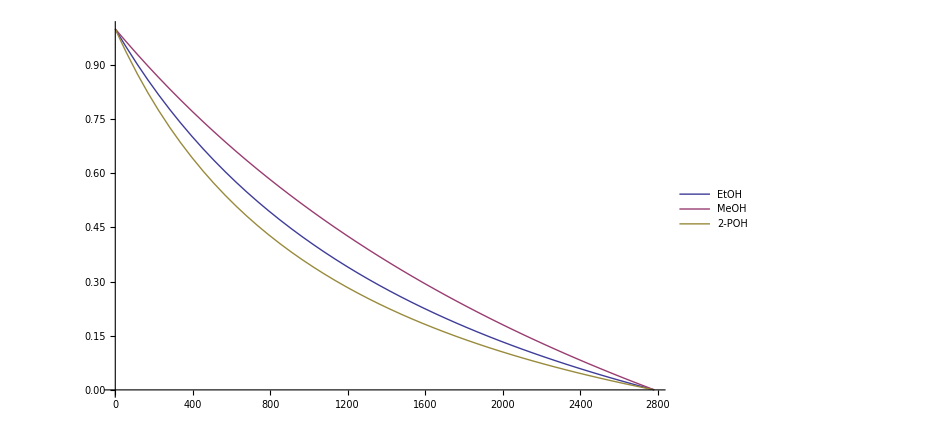

```mathematica
Plot[{1-MassPerEt[α],1-MassPerMe[α],1-MassPerP[α]},{α,0,2782},AxesLabel->Automatic,PlotLegends->{"EtOH","MeOH","2-POH"},PlotLabel->{"Mass Percent Water vs. Number of Molecules of Alcohol"}]
```

```mathematica
Clear[β]
```

```mathematica
Solve[(α*xXOH)/(α*xXOH+(β)*y)==a,α]
```

{{α→-(50094 a)/(-18 a-xXOH+a xXOH)}}

```mathematica
Solve[MassPerEt[α]==a,α]
```

{{α→-(25047 a)/(-23+14 a)}}

```mathematica
Solve[MassPerMe[α]==a,α]
```

{{α→-(25047 a)/(-16+7 a)}}

```mathematica
Solve[MassPerP[α]==a,α]
```

{{α→-(500940. a)/(-601.+421. a)}}

```mathematica
αEt[a_]=-(25047 a)/(-23+14 a);
```

```mathematica
αMe[a_]=-(25047 a)/(-16+7 a);
```

```mathematica
αP[a_]=-(500940. a)/(-601.+421. a);
```

```mathematica
coeffs[a_]={a,Ceiling[N[αEt[a],4]],Ceiling[N[αMe[a],4]],Ceiling[N[αP[a],4]]}
```

{a,Ceiling[-(25050. a)/(-23.+14. a)],Ceiling[-(25050. a)/(-16.+7. a)],Ceiling[-(500940. a)/(-601.+421. a)]}

```mathematica
TableForm[Table[coeffs[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules EtOH","Molecules MeOH","Molecules 2-POH"}}]
```

| Mass Fraction X-OH | Molecules EtOH | Molecules MeOH | Molecules 2-POH
 | 0. | 0 | 0 | 0
 | 0.1 | 116 | 164 | 90
 | 0.2 | 248 | 344 | 194
 | 0.3 | 400 | 541 | 317
 | 0.4 | 576 | 760 | 464
 | 0.5 | 783 | 1002 | 642
 | 0.6 | 1030 | 1274 | 863
 | 0.7 | 1329 | 1580 | 1145
 | 0.8 | 1699 | 1927 | 1517
 | 0.9 | 2168 | 2324 | 2030
 | 1. | 2783 | 2783 | 2783

```mathematica
Export["alcohols.txt",{{, "Mass Fraction X-OH", "Molecules EtOH", "Molecules MeOH", "Molecules 2-POH"}, {"", 0., 0, 0, 0}, {"", 0.1, 116, 164, 90}, {"", 0.2, 248, 344, 194}, {"", 0.3, 400, 541, 317}, {"", 0.4, 576, 760, 464}, {"", 0.5, 783, 1002, 642}, {"", 0.6, 1030, 1274, 863}, {"", 0.7, 1329, 1580, 1145}, {"", 0.8, 1699, 1927, 1517}, {"", 0.9, 2168, 2324, 2030}, {"", 1., 2783, 2783, 2783}}]
```

alcohols.txt

```mathematica
N[αEt[0]]
```

0.

```mathematica
coeffs2[a_]={a,Floor[2783-αEt[a]],Floor[2783-N[αMe[a],4]],Floor[N[2783-αP[a],4]]}
```

{a,2783+Floor[(25047 a)/(-23+14 a)],2783+Floor[(25050. a)/(-16.+7. a)],Floor[2783.+(500940. a)/(-601.+421. a)]}

```mathematica
TableForm[Table[coeffs2[a],{a,0,1,.10}],TableHeadings->{{},{"Mass Fraction X-OH","Molecules HOH (EtOH)","Molecules HOH (MeOH)","Molecules HOH (2-POH)"}}]
```

| Mass Fraction X-OH | Molecules HOH (EtOH) | Molecules HOH (MeOH) | Molecules HOH (2-POH)
 | 0. | 2783 | 2783 | 2783
 | 0.1 | 2667 | 2619 | 2693
 | 0.2 | 2535 | 2439 | 2589
 | 0.3 | 2383 | 2242 | 2466
 | 0.4 | 2207 | 2023 | 2319
 | 0.5 | 2000 | 1781 | 2141
 | 0.6 | 1753 | 1509 | 1920
 | 0.7 | 1454 | 1203 | 1638
 | 0.8 | 1084 | 856 | 1266
 | 0.9 | 615 | 459 | 753
 | 1. | 0 | 0 | 0

```mathematica
Export["aq.xlsx",{{"Mass Fraction X-OH", "Molecules HOH (EtOH)", "Molecules HOH (MeOH)", "Molecules HOH (2-POH)"}, {0., 2780, 2783, 2783}, {0.1, 2664, 2619, 2693}, {0.2, 2532, 2439, 2589}, {0.30000000000000004, 2380, 2242, 2466}, {0.4, 2204, 2023, 2319}, {0.5, 2000, 1781, 2141}, {0.6000000000000001, 1752, 1509, 1920}, {0.7000000000000001, 1452, 1203, 1638}, {0.8, 1084, 856, 1266}, {0.9, 612, 459, 753}, {1., 0, 0, 0}}]
```

$Failed